## Calculation of Franck-Condon Factors

Ben Schwyn

### Introduction

Spectroscopy is an important tool, and has been a great success for the application and testing of quantum theory.  Spectroscopy is a very precise way of discovering the elemental and molecular components of unknown substances in many fields from environmental science and biology labs, to advanced materials research. On known substances, spectroscopy can help determine the energy levels  and physical structure of atoms and molecules, allowing a better understanding of the processes reactions they go through. Throughout its history, spectroscopy has given inspiration and tests to quantum theory, beginning with the emission spectra of hydrogen and its subsequent explanation through the Bohr model.

Spectroscopy works by observing the absorption or emission of light from the absorption or release of energy related to the difference in energy levels. For individual atoms, this is usually the difference between the ground state valence electrons and excited electron states, usually resulting in energies corresponding to visual wavelengths. Higher energy wavelengths are often observed through the excitement of interior electrons.
	
In molecules, the spatial wavefunction of the nuclei becomes important. Different energy levels of this wavefunction determine the amount of vibration or relational movement between nuclei. In what is called the Born-Oppenheimer Approximation, there is the assumption that electronic and nuclear wavefunctions do not depend on the velocities of the electrons and nulcei, in which case the molecular wavefunction (ignoring spin) is separable:
	
	Ψ_Total=ψ_electronic*ψ_nuclear

The nuclear component of the wavefunction includes vibrational, translational and rotational components, which can often be factored.

ψ_electronic*ψ_nuclear=ψ_electronic*ψ_translational*ψ_rotational*ψ_vibrational

Roughly, transitions between energy levels in these different regions correspond to different energy photons. Electronic excitations are often visual, UV, or X-ray depending on the shell of the electron. Rotational energies are related to microwaves.

Closely related to the Born Oppenheimer Approximation is the Franck Condon Principle, which states that optical transitions in the electronic wavefunction occur fast enough that the nuclear wavefunction is not affected, and the vibrational transitions can be considered separately.

When considering the probability of an interaction with a photon and an electron in a molecule, the probability of the transition is given by

P(Ψ→Ψ')=(|⟨Ψ(r_1(…r)_N,R_1(…R)_N)χ|μ(r_1(…r)_N,R_1(…R)_N)|Ψ(r_1(…r)_N,R_1(…R)_N)' χ'⟩|)^2

Where μ is the electric dipole operator signifying that a photon, represented classically as electric field, interacts an electron in state ψ, and ψ'  is the final state of the electron. r_1(…r)_N are the spatial coordinates of the electrons,  R_1(…R)_N are the nucleons, and χ  is the spin of the electrons. Applying the Born Oppenheimer Approximation, and ignoring the rotational and translational components:

P(Ψ→Ψ')=(|⟨ψ_e(r_1(…r)_N) ψ_v(R_1(…R)_N)χ|μ|ψ_e(r_1(…r)_N)' ψ_v(R_1(…R)_N)' χ'⟩|)^2

The electric field will create a dipole out of the electrons and the nucleons:

=(|⟨ψ_e ψ_v χ|μ_e(r_1(…r)_N)+μ_N(R_1(…R)_N)|ψ_e' ψ_v' χ'⟩|)^2
(=|⟨ψ_e ψ_v χ|μ_e(r_1(…r)_N)ψ_e' ψ_v' χ'⟩+μ_N(R_1(…R)_N)|ψ_e' ψ_v' χ'⟩|)^2
=(|⟨ψ_v|ψ_v'⟩⟨ψ_e|μ_e|ψ_e'⟩⟨χ|χ'⟩+⟨ψ_e|ψ_e'⟩⟨ψ_v|μ_N|ψ_v'⟩⟨χ|χ'⟩|)^2

Here, the term with the nuclear dipole moment goes to zero due to the orthogonality of the electornic wavefunctions. For symmetric diatomic molecules .

=(|⟨ψ_v|ψ_v'⟩⟨ψ_e|μ_e|ψ_e'⟩+0*⟨ψ_v|0|ψ_v'⟩⟨χ|χ'⟩|)^2
P(Ψ→Ψ')=(|⟨ψ_v|ψ_v'⟩|)^2(|⟨ψ_e|μ_e|ψ_e'⟩⟨χ|χ'⟩|)^2

The final result is the orbital and spin selection rules multiplied by the factor called the Franck-Condon Factor (FCF), essentially a vibrational selection rule. For a particular orbital and spin excitation, the fcf modulates the intensities of the vibrational excitations.

The calculation of the integrals for a FCF is difficult, due to the large number of variables in a polyatomic molecule. For a diatomic molecule, the Morse potential can be approximated by a Harmonic potential and the FCF is only dependent on two position variables allowing the overlap integrals to be calculated analytically.

What follows is a visualization of the vibrational energy transitions, a calculation of the FCFs, and a example spectrum.visualization.

### MorsePotential

The Morse Potential is a model of the potential energy of a diatomic molecule.
μ is the reduced mass (with m1 and m2 the masses of the two molecules)
ω is the natural frequency
De is the dissasociation energy
re is the equilibrium bond length
R is the nuclear separation

#### Initialization

```mathematica
μ[m1_,m2_]:=(m1 m2)/(m1+m2)
k[m1_,m2_,ω_]:=μ[m1,m2]*ω^2
a[m1_,m2_,ω_,De_]:=√(k[m1,m2,ω]/(2 De))
```

```mathematica
MorsePotential[m1_,m2_,ω_,De_,R_,re_]:=De(1-ⅇ^(-a[m1,m2,ω,De](R-re)))^2
MorsePlot[m1_,m2_,ω_,De_,re_]:=Plot[MorsePotential[m1,m2,ω,De,R,re],{R,0,10},PlotRange->{0,10},Frame->True,FrameTicks->False,FrameLabel->{"Nuclear Separation","Energy"}]
```

#### Plot

```mathematica
Manipulate[
MorsePlot[m1,m2,ω,De,re],
{m1,1,5},{m2,1,5},{{ω,4.2},1,10},{{De,7},1,10},{{re,2},1,5}
]
```

### The Harmonic Oscillator as an approximation to theMorse Potential

#### Harmonic Oscillator Wavefunctions

```mathematica
HarmonicWaveFunction[x_,m1_,m2_,ω_,v_]:=((μ[m1,m2]*ω)/π)^(1/4)HermiteH[v,√(μ[m1,m2]*ω)x]  1/(√(2^v v!))Exp[-μ[m1,m2]*ω*x^2/2]
```

```mathematica
GroundState[x_,m1_,m2_,ω_]:=HarmonicWaveFunction[x,m1,m2,ω,0]
```

#### Initialization

```mathematica
HarmonicPotential[m1_,m2_,ω_,R_,re_]:=1/2 μ[m1,m2]*ω^2(R-re)^2
```

```mathematica
HarmonicEnergy[v_,ω_]:=ω*(v+1/2)
HPplot[m1_,m2_,ω_,re_]:=Plot[HarmonicPotential[m1,m2,ω,R,re],{R,0,15}]
EnergyLevels[m1_,m2_,ω_,re_,v_]:=Plot[HarmonicEnergy[v,ω],{x,re-√((2(v+1/2))/(μ[m1,m2]*ω)),re+√((2(v+1/2))/(μ[m1,m2]*ω))}]
MorsePlot2[m1_,m2_,ω_,De_,re_]:=Plot[MorsePotential[m1,m2,ω,De,R,re],{R,0,15},PlotRange->{0,20},FrameTicks->None,Frame->True,FrameLabel->{"Nuclear Separation","Energy"}]
```

#### Plot

```mathematica
Quiet[
Manipulate[
Show[
MorsePlot2[m1,m2,ω,De,re],
HPplot[m1,m2,ω,re],
Table[
EnergyLevels[m1,m2,ω,re,v],{v,0,20}
]
],{{m1,1},1,5},{{m2,1},1,5},{{ω,4},1.5,8},{{re,3},1,8},{{De,15},1,20}
]
]
```

### Vibronic Transitions in The Harmonic Oscillator

#### Initialization

```mathematica
Bound[m1_,m2_,v_,ω_]:=√((2(v+1/2))/(μ[m1,m2]*ω))

EnergyLevelsExcited[m1_,m2_,ω_,re2_,v_,ΔE_]:=Plot[HarmonicEnergy[v,ω]+ΔE,{x,re2-Bound[m1,m2,v,ω],re2+Bound[m1,m2,v,ω]},PlotStyle->Red,PlotRange->{0,20}]

HPplot2[m1_,m2_,ω_,re_]:=Plot[HarmonicPotential[m1,m2,ω,R,re],{R,0,10},PlotRange->{0,20},PlotStyle->Thick,Frame->True,FrameTicks->False,FrameLabel->{"Nuclear Separation","Energy"}]

HPplotExcited[m1_,m2_,ω_,re2_,ΔE_]:=Plot[HarmonicPotential[m1,m2,ω,R,re2]+ΔE,{R,0,10},PlotStyle->{Red,Thick}]
```

```mathematica
PlotGroundStateProbability[re_,m1_,m2_,ω_]:=Plot[GroundState[x-re,m1,m2,ω]^2+HarmonicEnergy[0,ω],{x,re-Bound[m1,m2,0,ω]-.5,re+Bound[m1,m2,0,ω]+.5},Filling->HarmonicEnergy[0,ω]]
```

```mathematica
ψv[x_,α_,v_]:=(α/π)^(1/4)HermiteH[v,√α x]  1/(√(2^v v!))Exp[-α*x^2/2]

ExcitedWaveFunctions[x_,m1_,m2_,ω_,v_]:=ψv[x,μ[m1,m2]*ω,v]

PlotExcitedWaveFunctionsProbability[re2_,m1_,m2_,ω_,v_,ΔE_]:=Plot[ExcitedWaveFunctions[x-re2,m1,m2,ω,v]^2+HarmonicEnergy[v,ω]+ΔE,{x,re2-Bound[m1,m2,v,ω]-.5,re2+Bound[m1,m2,v,ω]+.5},PlotStyle->Black,Filling->HarmonicEnergy[v,ω]+ΔE]
```

#### Plot

When the initial ground state peak lines up with one of the excited peaks, then that maximizes the transition to that vibrational level. The plot starts out with the most likely transition of v0->v1.

```mathematica
Manipulate[
Show[
HPplot2[m1,m2,ω,re],
HPplotExcited[m1,m2,ω,re2,ΔE],
Table[
EnergyLevels[m1,m2,ω,re,v],{v,0,20}
],
Table[
EnergyLevelsExcited[m1,m2,ω,re2,v,ΔE],{v,0,20}
],
Table[
PlotExcitedWaveFunctionsProbability[re2,m1,m2,ω,v,ΔE],{v,0,6}
],
PlotGroundStateProbability[re,m1,m2,ω],
Graphics[
Arrow[
{{re,HarmonicEnergy[0,ω]},{re,HarmonicPotential[m1,m2,ω,re,re2]+ΔE+2}}
]
]
],{{m1,1},1,5},{{m2,1},1,5},{{ω,4},2,5},{{re,2},1.5,2.5},{{re2,2.845},1,4},{{ΔE,5},1,10}
]
```

### Calculation of Franck-Condon Factors

#### Wavefunctions

```mathematica
ψv[x_,α_,v_]:=(α/π)^(1/4)HermiteH[v,√α x]  1/(√(2^v v!))Exp[-α*x^2/2]
```

Δr is the difference in equilibrium bond length between the exicted and ground state.

```mathematica
GroundStateFC[x_,α_]:=ψv[x,α,0]
```

```mathematica
ψ0[x_,Δr_,α_]:=ψv[x-Δr,α,0]
ψ1[x_,Δr_,α_]:=ψv[x-Δr,α,1]
ψ2[x_,Δr_,α_]:=ψv[x-Δr,α,2]
ψ3[x_,Δr_,α_]:=ψv[x-Δr,α,3]
ψ4[x_,Δr_,α_]:=ψv[x-Δr,α,4]
ψ5[x_,Δr_,α_]:=ψv[x-Δr,α,5]
ψ6[x_,Δr_,α_]:=ψv[x-Δr,α,6]
```

#### Integration Factors

```mathematica
fcf0[Δr_]:=Integrate[GroundStateFC[x,α]*ψ0[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf1[Δr_]:=Integrate[GroundStateFC[x,α]*ψ1[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf2[Δr_]:=Integrate[GroundStateFC[x,α]*ψ2[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf3[Δr_]:=Integrate[GroundStateFC[x,α]*ψ3[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf4[Δr_]:=Integrate[GroundStateFC[x,α]*ψ4[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf5[Δr_]:=Integrate[GroundStateFC[x,α]*ψ5[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
fcf6[Δr_]:=Integrate[GroundStateFC[x,α]*ψ6[x,Δr,α],{x,Δr-3.5,Δr+3.5}]
```

```mathematica
fcflist[Δr_]:=N[Through[{fcf0,fcf1,fcf2,fcf3,fcf4,fcf5,fcf6}[Δr]]]
```

#### initialization of variables

Here I assumed an electronic transition of 250 nm with a guassian approximation to curve and a vibrational component of 1200 cm^-1 for the 0-0 transition. This is the C=C bond in ethene.

```mathematica
α:=1
λ0:=250
h:=6.62 *10^-34
clight:=3*10^8
λmin:=200
λmax:=300
ν:=1200
ω:=clight*ν*100
Δλ:=5
σ:=Δλ/2.35
```

```mathematica
Enorm:=(h*clight*10^9)/λ0
krange:=Range[0,6]
Ek=Enorm+krange*h*ω
λcenter:=(h*clight*10^9)/Ek
```

{7.944×10^-19,8.18232×10^-19,8.42064×10^-19,8.65896×10^-19,8.89728×10^-19,9.1356×10^-19,9.37392×10^-19}

```mathematica
maxpts:=200
λincr:=(λmax-λmin)/maxpts
step:=Range[0,maxpts]
λ:=λ=λmin+step*λincr
```

```mathematica
NumericalGuassian:=Table[ⅇ^(-(λ[[q]]-λcenter[[w]])^2/(2*σ^2)),{w,7},{q,maxpts}]
```

#### Plots

{0.778792,-0.550651,0.275191,-0.111979,0.0387568,-0.0106605,0.000456247}

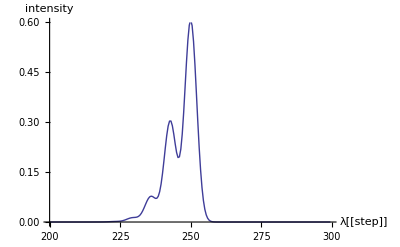

```mathematica
fcflist[1]
NumGaussSum1:=NumGaussSum1=Sum[NumericalGuassian[[w]]*(fcflist[1][[w]])^2,{w,1,7}]
NumericalIntensity1:=NumericalIntensity1=Table[{λ[[y]],NumGaussSum1[[y]]},{y,1,maxpts}]
ListPlot[NumericalIntensity1,{PlotJoined->True,AxesLabel->{"λ[[step]]","intensity"}},PlotRange->{0,.6}]
```

{0.569754,-0.604197,0.452735,-0.276109,0.143863,-0.0633215,0.0193524}

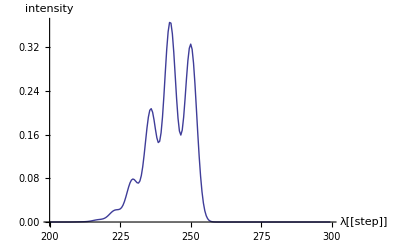

```mathematica
fcflist[1.5]
NumGaussSum15:=NumGaussSum15=Sum[NumericalGuassian[[w]]*(fcflist[1.5][[w]])^2,{w,1,7}]
NumericalIntensity15:=NumericalIntensity15=Table[{λ[[y]],NumGaussSum15[[y]]},{y,1,maxpts}]
ListPlot[NumericalIntensity15,{PlotJoined->True,AxesLabel->{"λ","intensity"}}]
```

{0.367805,-0.519871,0.518879,-0.420945,0.291499,-0.17256,0.0802772}

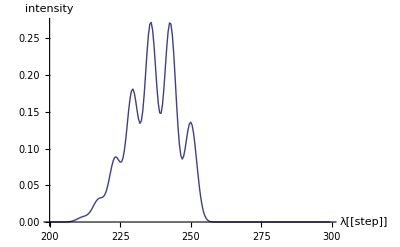

```mathematica
fcflist[2]
NumGaussSum2:=NumGaussSum2=Sum[NumericalGuassian[[w]]*(fcflist[2][[w]])^2,{w,1,7}]
NumericalIntensity2:=NumericalIntensity2=Table[{λ[[y]],NumGaussSum2[[y]]},{y,1,maxpts}]
ListPlot[NumericalIntensity2,{PlotJoined->True,AxesLabel->{"λ[[step]]","intensity"}}]
```

{0.209458,-0.369744,0.460327,-0.464741,0.399279,-0.293612,0.175745}

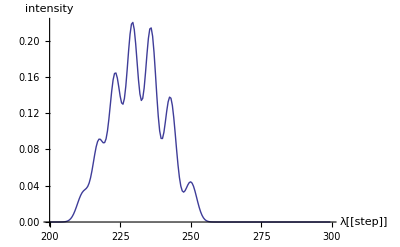

```mathematica
fcflist[2.5]
NumGaussSum25:=NumGaussSum25=Sum[NumericalGuassian[[w]]*(fcflist[2.5][[w]])^2,{w,1,7}]
NumericalIntensity25:=Table[{λ[[y]],NumGaussSum25[[y]]},{y,1,maxpts}]
ListPlot[NumericalIntensity25,{PlotJoined->True,AxesLabel->{"λ[[step]]","intensity"}}]
```

{0.105153,-0.222292,0.330743,-0.397687,0.405082,-0.352218,0.25243}

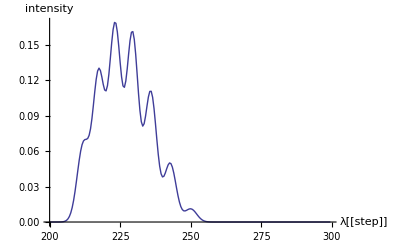

```mathematica
fcflist[3]
NumGaussSum3:=NumGaussSum3=Sum[NumericalGuassian[[w]]*(fcflist[3][[w]])^2,{w,1,7}]
NumericalIntensity3:=Table[{λ[[y]],NumGaussSum3[[y]]},{y,1,maxpts}]
ListPlot[NumericalIntensity3,{PlotJoined->True,AxesLabel->{"λ[[step]]","intensity"}}]
```

#### Summary

As the difference in bond distance goes from 1 to 3 (with units of (ℏ/ωμ)^(1/2) you can see most likely vibrational mode goes from v0->v0 to v0->v5.